```mathematica
nx[x_, u_] := - E ^(-2Abs[x + u])
```

```mathematica
n[x_] := E ^(- 2Abs[x])
```

```mathematica
kf[x_] := Pi n[x]
```

```mathematica
nxlda[x_, u_] := -n[x](Sin[kf[x] Abs[u]]/(kf[x] Abs[u]))^2
```

0

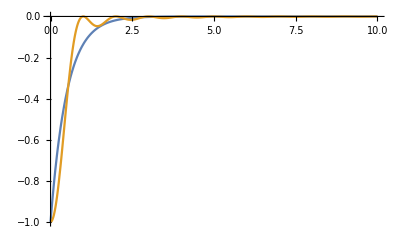

```mathematica
x1 = 0
Plot[{nx[x1, u], nxlda[x1, u]}, {u,0, 10}, PlotRange->All]
```

```mathematica
nxsym[x_, u_] := 1/2(nx[x,u] +nx[x,-u])
```

```mathematica
nxldasym[x_,u_] := 1/2(nxlda[x,u] + nxlda[x, -u])
```

```mathematica
Plot[{nxsym[x1,u], nxldasym[x1, u]}, {u,0, 10}, PlotRange->All]
```

-Graphics-

```mathematica
enex[u_] := NIntegrate[2 nxsym[x,u] n[x], {x, -Infinity, Infinity}]
```

```mathematica
enexlda[u_] := NIntegrate[2 nxldasym[x,u] n[x], {x, -Infinity, Infinity}]
```

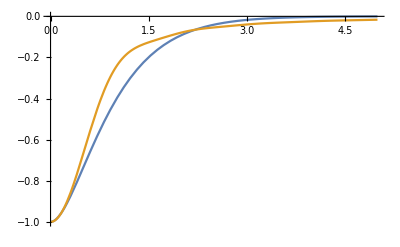

```mathematica
Plot[{enex[u], enexlda[u]}, {u, 0, 5}, PlotRange->All]
```